```mathematica
Today
```

Sat 21 Apr 2018

# Snakes and Ladders

Found on the web using Google Image search, here is one free example of the Snakes and Ladders game. Although if you want to be pedantic about it, Snakes and Ladders is not a game or even a puzzle, since the players don’t get to make any decisions that could affect the course of the game, but can only keep rolling the die and watch the game go until the lucky winner finally reaches the goal tile 100. The game is really a randomized automaton that is too lazy to even make its own moves, so it attracts the hapless little human players to carry out the actual motions as its arms.

```mathematica
SetDirectory["/Users/ilkkakokkarinen/Desktop/Ilkka/WolframExamples/"];
Import["snakesladders.jpg"]
```

-Graphics-

To convert this game into a computable form, we need to encode the gameboard into a Mathematica list structure. To do this, we define a function that gives the number of the tile in the given row and column of the board. The rows are numbered from 1 to 10 going up, and the columns are numbered from 1 to 10 going right. To verify that the formula is correct, we can print the two-dimensional table generated using that function.

```mathematica
tileIdx[row_,col_] := 10 * (row  - 1) + If[Mod[Floor[row / 10],2]==0, col, 11 - col];
Table[tileIdx[row,col], {row, 10, 1, -1}, {col, 1, 10}] // MatrixForm
```

(100 | 99 | 98 | 97 | 96 | 95 | 94 | 93 | 92 | 91
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10)

Next, a function that expresses the structure of the snakes and the ladders gameboard by telling which tile the player actually ends up when moving into that tile. Snakes are those tiles that move the player to a lower position, whereas ladders are those tiles that move a player to a higher position. All other tiles can be thought of as snakes (or ladders, depending on your general outlook on life) of zero length that keep you in that same tile.

```mathematica
board = {
{100, 41, 98, 97, 96, 95, 94, 93, 92, 91},
{81, 82, 83, 84, 85, 86, 87, 88, 53, 90},
{80, 79, 78, 77, 45, 75, 92, 73, 72, 71},
{61, 81, 63, 64, 65, 45, 67, 68, 69, 70},
{60, 59, 58, 57, 56, 55, 31, 53, 52, 51},
{41, 63, 18, 44, 45, 46, 47, 48, 49, 69},
{03, 39, 38, 37, 36, 35, 34, 39, 32, 31},
{21, 22, 23, 24, 25, 26, 05, 28, 29, 30},
{20, 19, 18, 17, 16, 15, 14, 13, 12, 11},
{01, 02, 03, 25, 05, 06, 07, 08, 09, 10}
};
```

Even though the gameboard is drawn two-dimensionally to take less space and be easier for our human eyes to follow, its state space of tiles is really a one-dimensional sequence of integers 1 to 100. To convert between these two representations, we define two functions that give the row and the column coordinates that the given tile is located on the board.

```mathematica
row[idx_] := 10 - Floor[(idx-1) / 10];
col[idx_] := With[{c = Mod[(idx-1), 10]}, If[Mod[row[idx],2] == 1, 10 - c, c + 1]];
```

Now we can create a one-dimensional list where the tiles are numbered in sequence from 1 to 100. We use the variation of rules where the goal state must be hit exactly, and otherwise the player bounces back the number of tiles past the goal. The easier version where the goal is reached by getting past it, in style of the game of backgammon, could be implemented by changing the formula for first branch of the If inside the move function to be just the constant 100.

```mathematica
target =Table[board[[row[idx], col[idx]]], {idx, 1, 100}];
move[idx_, step_] := target[[If[idx + step > 100, 200 - (idx + step), idx + step]]];
```

The state space of the Snakes and Ladders game forms an absorbing Markov chain, which is really only a fancy way to say that the “Markovian” probabilities for where each roll of the die takes the player from the current tile are independent of the past history that led the player to that tile, and the “absorbing” part means that there are some tiles that once you enter, you will never leave since the game is over, until at least when you reset the game back to the initial state. The goal tile 100 is absorbing and causes all movement and the game to end. Even though the players do not have any decisions to make, it is still interesting and nontrivial to ask how many moves it will take on average to reach the goal 100 starting from some particular state. Again, due to the Markov property of this system, only the current state matters for this calculation, as the path that the player took to get to that state is irrelevant. We start by defining the symbolic Bellman equation for each tile so that this equation connects the number of moves needed to reach the goal starting from that tile to the corresponding numbers of the tiles that can be reached from that tile with one roll of die.

```mathematica
var[idx_] := Subscript[m, idx];
bellman[idx_ /; idx > 99] := var[idx] == 0;
bellman[idx_ /; idx < 100] := Subscript[m, idx] == 1 + Apply[Plus,Table[1/6 * var[move[idx,i]], {i, 1,6}]];
```

For example, the symbolic equation that tells us for how many moves are needed to reach the goal starting from tile 1 is

```mathematica
bellman[1]
```

m_1==1+m_2/6+m_3/6+m_5/6+m_6/6+m_7/6+m_25/6

These equations together comprise a set of one hundred linear equations for the one hundred unknown variables. We humans might balk at the idea of solving those by hand, but Mathematica should have no problem in solving even a hundred times as many. The powerful function Solve returns the list of all solutions as substitution rules. Since we know that this linear system should have precisely one solution, we can just take the First (and the only) element of the solution list.

```mathematica
sol = First[Solve[Table[bellman[idx],{idx,1,100}],Table[var[idx], {idx, 1, 100}]]];
```

The exact solutions involve pretty big fractions, which of course also are no problem for the symbolic nature of Mathematica. The exact solution is such an unwieldy fraction for us humans that it is better to use the handy Mathematica operator N that can provide the numerical approximation for any symbolic expression up to the desired number of significant digits. Doing so, we find out that it will take an average of almost 89 moves to reach the goal starting from initial tile 1.

```mathematica
sol1 = var[1] /. sol
N[sol1, 4]
```

449424144225935400613737039431919240616161311146725619300711351/5051932675637140069000479132454551431017215134626975975673640

88.96

The snakes seem to be swallowing the players quite hungrily along the route, since even when you have reached the state 98 that is only two steps away from the goal, it will still take an average of little over 50 moves to reach the goal. Of the six possible rolls of the die at that point, only one of them takes you to the goal, two cause you fall all the way down to tile 41, and the other three take you the tiles 98, 97 and 96.

```mathematica
bellman[98] /. sol
sol98 = var[98] /. sol
N[sol98, 4]
```

True

3525930192081518882689255650032157899102942632414967145362886/70165731606071389847228876839646547653016876869819110773245

50.25

At this point, we might as well print out the expected move count matrix for the entire gameboard.

```mathematica
Table[N[var[target[[tileIdx[row,col]]]] /. sol,4], {row, 10, 1, -1}, {col, 1, 10}] // MatrixForm
```

(0 | 72.38 | 50.25 | 50.25 | 50.25 | 50.25 | 46.56 | 54.32 | 51.32 | 51.49
58.97 | 58.4 | 59.86 | 58.69 | 57.67 | 56.76 | 56.41 | 55. | 68.63 | 51.7
62.19 | 61.91 | 61.61 | 51.32 | 62.39 | 69.5 | 60.44 | 60.19 | 59.83 | 59.39
65.16 | 58.97 | 64.92 | 64.58 | 64.24 | 69.5 | 62.78 | 61.14 | 61.32 | 62.49
69.95 | 69.25 | 68.63 | 79.51 | 66.14 | 65.12 | 65.09 | 65.02 | 64.9 | 65.56
72.38 | 64.92 | 85.6 | 69.43 | 69.5 | 69.47 | 69.35 | 70.8 | 70.13 | 61.32
79.51 | 79.18 | 76.1 | 80.55 | 79.38 | 77.32 | 78.5 | 77.2 | 76.1 | 88.8
85.45 | 84.69 | 84.03 | 83.41 | 82.85 | 82.33 | 89.36 | 80.18 | 80.07 | 79.67
87.66 | 87.36 | 87.05 | 86.73 | 86.55 | 86.28 | 85.96 | 85.6 | 85.2 | 84.79
88.96 | 88.89 | 88.8 | 82.85 | 89.36 | 89.08 | 88.79 | 88.49 | 88.21 | 87.94)

Using the full power of Mathematica’s built-in symbolic equation solver Solve might be considered to be a bit of overkill for a system of simple linear equations. Markov chains are traditionally expressed as transition matrices whose each entry gives the probability from moving from the row state to the the column state. The dimensions of this transition matrix will now be 100-by-100, since the Snakes and Ladders board has 100 tiles. However, this transition matrix will be quite sparse since most of those entries will be zero values, seeing that from each individual tile there exists a nonzero possibility to advance to only at most six other tiles.

```mathematica
neighbours[i_] := Table[move[i, step], {step, 1, 6}];
prob[i_, j_] := Count[neighbours[i], j] / 6;
pm = Table[prob[i,j], {i, 1, 100}, {j, 1, 100}];
```

Markov chain properties can now be computed from this transition matrix, giving us the same table of expected path lengths as the symbolic equation solver. The linear algebra formulas were taken from the Wikipedia page “Absorbing Markov Chain”. The submatrix pq contains the transition probabilities of the non-absorbing tiles 1 to 99, from which the path lengths can be computed with basic linear algebra. Mathematica has, of course, a built in function for all such operations of matrix algebra.

```mathematica
pq = Take[pm,{1, 99}, {1, 99}];
pn= Inverse[IdentityMatrix[99] - pq];
expectedSteps = Join[First[Transpose[pn . Transpose[{Table[1, {i, 1, 99}]}]]],{0}];
Table[N[expectedSteps[[target[[tileIdx[row,col]]]]],4], {row, 10, 1, -1}, {col, 1, 10}] // MatrixForm
```

(0 | 72.38 | 50.25 | 50.25 | 50.25 | 50.25 | 46.56 | 54.32 | 51.32 | 51.49
58.97 | 58.4 | 59.86 | 58.69 | 57.67 | 56.76 | 56.41 | 55. | 68.63 | 51.7
62.19 | 61.91 | 61.61 | 51.32 | 62.39 | 69.5 | 60.44 | 60.19 | 59.83 | 59.39
65.16 | 58.97 | 64.92 | 64.58 | 64.24 | 69.5 | 62.78 | 61.14 | 61.32 | 62.49
69.95 | 69.25 | 68.63 | 79.51 | 66.14 | 65.12 | 65.09 | 65.02 | 64.9 | 65.56
72.38 | 64.92 | 85.6 | 69.43 | 69.5 | 69.47 | 69.35 | 70.8 | 70.13 | 61.32
79.51 | 79.18 | 76.1 | 80.55 | 79.38 | 77.32 | 78.5 | 77.2 | 76.1 | 88.8
85.45 | 84.69 | 84.03 | 83.41 | 82.85 | 82.33 | 89.36 | 80.18 | 80.07 | 79.67
87.66 | 87.36 | 87.05 | 86.73 | 86.55 | 86.28 | 85.96 | 85.6 | 85.2 | 84.79
88.96 | 88.89 | 88.8 | 82.85 | 89.36 | 89.08 | 88.79 | 88.49 | 88.21 | 87.94)

But let us next pretend that instead of Mathematica, we happened to be working in some lower level programming language where symbolic expressions, let alone advanced linear algebra and higher level equation solvers, would not be not baked into the language or its standard library. Needing only an approximate numeral solution to a Markov chain, we can approximate the expected number of moves needed to reach the goal starting from the given tile by generating a large number of paths using random dice rolls, and for each tile, computing the average number of moves needed to reach the goal from that tile. The function path generates a random list of tiles starting from the given tile all the way up to the goal, to be used as a training sample for the every-visit Monte Carlo method below. Such lists where each element is computed based on the previous element regardless of any earlier elements are easy to generate using the NestWhileList built-in function. (In fact, this function can optionally be made to compute each element from the previous k elements for any arbitrary fixed k, as explained in its documentation.) To eyeball the variance in these random paths form the sheer effect of luck, we can plot a histogram of the lengths of one thousand random paths starting from tile 1.

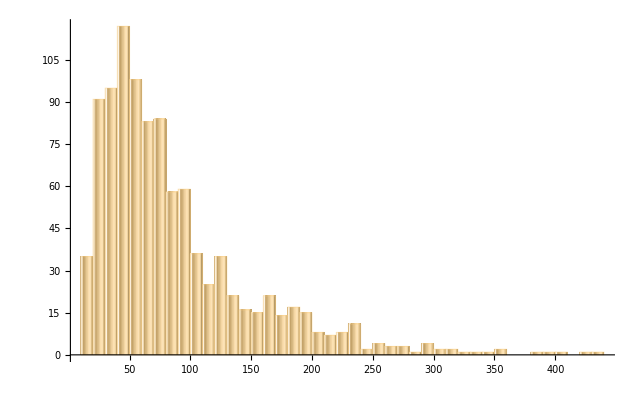

{21559/250,(2 √(131912822/555))/15,7855541749383/(527651288 √65956411)}

```mathematica
path[i_] :=NestWhileList[(move[#,RandomInteger[{1, 6}]])&, target[[i]], (# < 100)&];
samplePaths =Table[Length[path[1]] - 1, {k, 1, 1000}]; 
Histogram[samplePaths, "FreedmanDiaconis", ChartElementFunction -> "GlassRectangle"]
{Mean[samplePaths], StandardDeviation[samplePaths], Skewness[samplePaths]}
```

The function everyVisitMonteCarlo internally uses the path function to generate the desired number of random paths (each path starts from a different tile to guarantee that every tile will be visited at least once during these random journeys) and keeps a running tally of how many times each tile has been visited and the total sum of path lengths that have been observed to start from that tile. Every randomly generated path therefore gives us data not just for the starting tile, but for every tile encountered along the way, again made possible by the Markov property of this game where the history that led the player to the particular tile does not have an effect to the future of that tile. Given a sufficient number of sample paths, the results are pretty close to the symbolically solved exact solutions, as we can see by printing the matrix of the approximate solution and comparing it to the exact solution above.

```mathematica
everyVisitMonteCarlo[trials_] := Module[{visits, totals, i,j, p, tile},
visits = Table[0, {k, 1, 100}];
totals = Table[0, {k, 1, 100}];
For[i = 0, i < trials, i++,
p = path[Mod[i, 100] + 1];
For[j = 1, j <= Length[p], j++,
tile = p[[j]];
visits[[tile]]++;
totals[[tile]] = totals[[tile]] + Length[p] - j;
];
];
totals / (visits /. 0 -> 1)
];

With[{ tt = everyVisitMonteCarlo[100000]}, Table[N[tt[[target[[tileIdx[row,col]]]]],4], {row, 10, 1, -1}, {col, 1, 10}]] // MatrixForm
```

(0 | 71.6 | 49.68 | 49.79 | 49.48 | 49.44 | 45.99 | 53.55 | 50.81 | 50.29
58.13 | 57.86 | 58.78 | 57.91 | 56.73 | 55.98 | 55.66 | 54.54 | 67.89 | 51.08
61.62 | 61.51 | 60.84 | 50.81 | 61.53 | 69.12 | 59.65 | 59.32 | 59.12 | 58.89
64.29 | 58.13 | 64.28 | 64.12 | 63.61 | 69.12 | 62.71 | 60.39 | 60.67 | 61.48
69.47 | 68.83 | 67.89 | 78.65 | 65.74 | 64.39 | 64.22 | 64.46 | 64.5 | 65.42
71.6 | 64.28 | 84.64 | 68.43 | 69.12 | 68.78 | 68.45 | 69.96 | 69.62 | 60.67
78.65 | 78.51 | 75.3 | 79.21 | 78.44 | 76.42 | 78. | 76.45 | 75.3 | 87.79
84.47 | 83.68 | 83.13 | 82.55 | 82.24 | 81.45 | 88.62 | 78.98 | 78.76 | 79.01
86.85 | 86.96 | 86.35 | 85.87 | 85.9 | 85.6 | 85.36 | 84.64 | 84.84 | 83.96
90.52 | 87.71 | 87.79 | 82.24 | 88.62 | 88.79 | 88.77 | 87.74 | 87.3 | 87.57)

The reader might now wonder why anybody would ever settle for a slower and less accurate algorithm when nice and exact symbolic solutions are so readily available. If the problem is solving the expected number of moves to get through Snakes and Ladders, there would indeed be very little reason to do so. But in general, computing such exact solutions requires complete knowledge of the transition probabilities of the system, which we happen to know in this problem based on our knowledge of the structure of Snakes and Ladders game board and the assumed behaviour of an ordinary six-sided die.
Were this underlying structure and the corresponding transition probabilities of the Markovian system that we want to model hidden from our eyes, as is the case for the majority of interesting real world problems, such exact symbolic solutions would not be possible to calculate from these unknown transition probabilities. (Given enough training samples, the transition probabilities between states could be approximated by building up a complex model of transition probabilities observed from the training samples, but why bother?) The huge advantage of the every-visit Monte Carlo method is that it does not need those probabilities, as long as the underlying system can be asked to produce new training samples from the distribution that follows those probabilities. Given enough training samples generated from this underlying actual probability distribution of possible moves, the estimates produced by the Monte Carlo algorithm are guaranteed to converge to the exact solutions.